## Fitting sigma dan eden

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\efpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\efpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\efpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\efpc_gup1E-9.dat

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\sfpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\sfpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\sfpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

D:\Dropbox\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\EOS_alka\sfpc_gup1E-9.dat

### fitting anisotropik

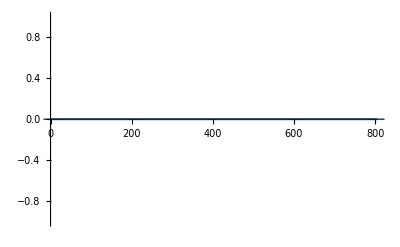

0.

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*)]
```

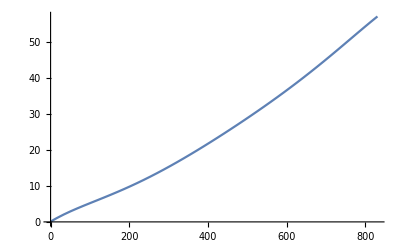

0.07155239813179404 + 0.06606791761347486*P0 - 
     -  0.00024112533580554287*P0**2 + 1.143510757936114e-6*P0**3 - 
     -  2.2910564964032e-9*P0**4 + 2.2151475945322894e-12*P0**5 - 
     -  8.284546815733482e-16*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*)]
```

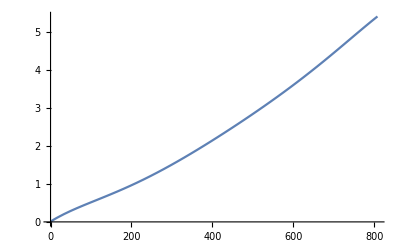

0.00893216184253268 + 0.0066138230853899135*P0 - 
     -  0.00002547856239766327*P0**2 + 1.227701424673366e-7*P0**3 - 
     -  2.525768285081147e-10*P0**4 + 2.5092894933230487e-13*P0**5 - 
     -  9.644098826004996e-17*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*)]
```

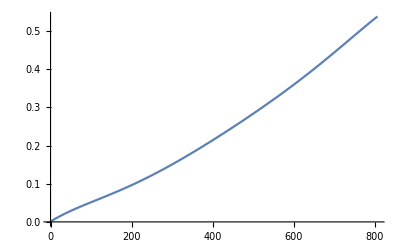

0.0009109253091662184 + 0.0006614884992791607*P0 - 
     -  2.562440474996395e-6*P0**2 + 1.2369135151340834e-8*P0**3 - 
     -  2.5518866105304432e-11*P0**4 + 2.542548182407993e-14*P0**5 - 
     -  9.800236597274048e-18*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*)]
```

### fitting energy density GUP 0E0

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]+5]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]-4;;Dimensions[data][[1]]]];
```

#### GUP 0E0 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+2]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

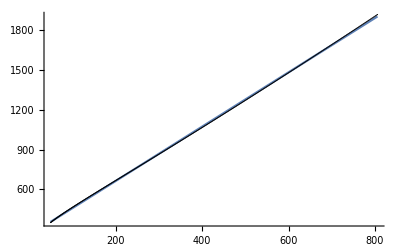

252.735+2.05179 P0

```mathematica
fitted=Fit[dataInnerCore,{1,P0},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP0E0=fitted
```

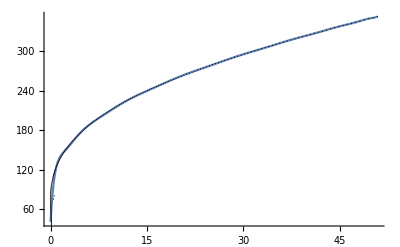

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP0E0=fitted;
```

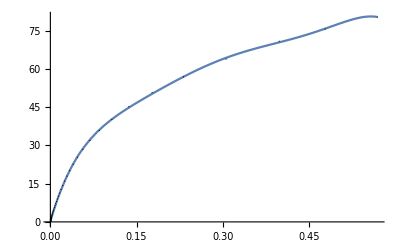

0.213861+768.938 P0-6179.09 P0^2+31192. P0^3-85373.6 P0^4+117009. P0^5-62844.5 P0^6

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP0E0=fitted
```

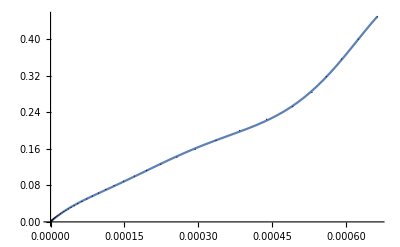

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP0E0=fitted
```

#### Cek hasilnya

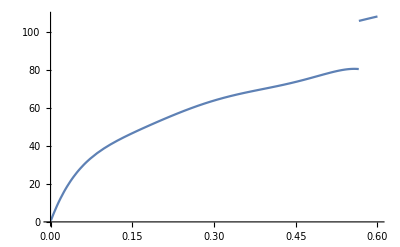

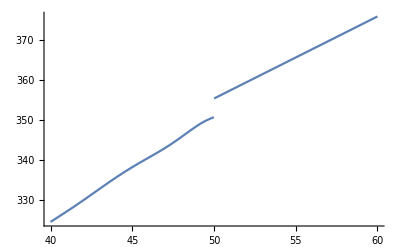

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP0E0;
FED2[P0_]=fitOuterCoreGUP0E0;
FED3[P0_]=fitInnerCrustGUP0E0;
FED4[P0_]=fitOuterCrustGUP0E0;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP0E0//FortranForm
```

252.7351203007992 + 2.0517873998109133*P0

```mathematica
fitOuterCoreGUP0E0//FortranForm
```

40.72822519163616 + 172.88564172842007*P0 - 129.75665741187734*P0**2 + 
     -  57.21198616046201*P0**3 - 15.6150708008523*P0**4 + 
     -  2.8354313027185887*P0**5 - 0.3602847077751246*P0**6 + 
     -  0.03316049472454524*P0**7 - 0.0022626453096747964*P0**8 + 
     -  0.00011613173543073938*P0**9 - 4.5162772145274745e-6*P0**10 + 
     -  1.3312210942573273e-7*P0**11 - 2.952609024402367e-9*P0**12 + 
     -  4.845080539678656e-11*P0**13 - 5.701316398676422e-13*P0**14 + 
     -  4.5477089999551786e-15*P0**15 - 2.2015407469797255e-17*P0**16 + 
     -  4.881799449675595e-20*P0**17

```mathematica
fitInnerCrustGUP0E0//FortranForm
```

0.2138614869659046 + 768.9378464621362*P0 - 6179.085226412627*P0**2 + 
     -  31192.024180740616*P0**3 - 85373.61029759394*P0**4 + 
     -  117008.53995402799*P0**5 - 62844.457041598056*P0**6

```mathematica
fitOuterCrustGUP0E0//FortranForm
```

0.00020663104786823767 + 985.7550962048155*P0 - 
     -  6.452649548410661e6*P0**2 + 4.045493650683346e10*P0**3 - 
     -  1.2422017897554195e14*P0**4 + 1.765493095354902e17*P0**5 - 
     -  9.1529417012139e19*P0**6

### fitting energy density GUP 1Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]+5]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]-4;;Dimensions[data][[1]]]];
```

#### GUP 1Em7 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+2]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

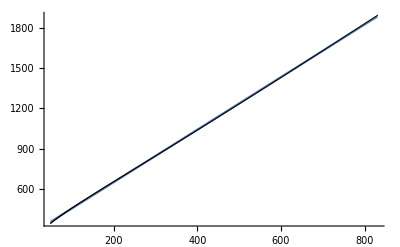

257.98+1.95692 P0

```mathematica
fitted=Fit[dataInnerCore,{1,P0},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em7=fitted
```

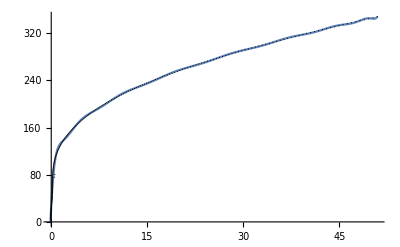

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em7=fitted;
```

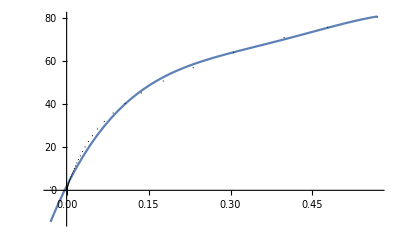

1.95562+510.157 P0-1731.01 P0^2+2942.34 P0^3-1842.41 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em7=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

#### Cek hasilnya

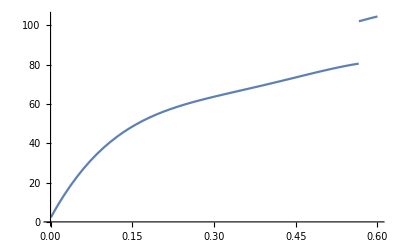

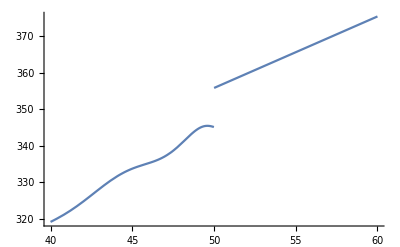

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em7;
FED2[P0_]=fitOuterCoreGUP1Em7;
FED3[P0_]=fitInnerCrustGUP1Em7;
FED4[P0_]=fitOuterCrustGUP1Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em7//FortranForm
```

257.9799384090066 + 1.9569165063025655*P0

```mathematica
fitOuterCoreGUP1Em7//FortranForm
```

26.792963384820982 + 212.32723839848072*P0 - 183.05922154778605*P0**2 + 
     -  89.85873533958548*P0**3 - 26.782581281061287*P0**4 + 
     -  5.234534531022756*P0**5 - 0.7079405866302086*P0**6 + 
     -  0.0687440360332156*P0**7 - 0.004913868423197951*P0**8 + 
     -  0.00026269453845358007*P0**9 - 0.000010590337777766127*P0**10 + 
     -  3.2231720681360846e-7*P0**11 - 7.356748971512561e-9*P0**12 + 
     -  1.2387524537448806e-10*P0**13 - 1.4920818654276785e-12*P0**14 + 
     -  1.2156733044662518e-14*P0**15 - 5.999956952734376e-17*P0**16 + 
     -  1.3542143049639314e-19*P0**17

```mathematica
fitInnerCrustGUP1Em7//FortranForm
```

1.9556157223144337 + 510.1571753657856*P0 - 1731.0073225480944*P0**2 + 
     -  2942.342342591839*P0**3 - 1842.4124908739573*P0**4

```mathematica
fitOuterCrustGUP1Em7//FortranForm
```

0.00020663104786823767 + 985.7550962048155*P0 - 
     -  6.452649548410661e6*P0**2 + 4.045493650683346e10*P0**3 - 
     -  1.2422017897554195e14*P0**4 + 1.765493095354902e17*P0**5 - 
     -  9.1529417012139e19*P0**6

### fitting energy density GUP 1Em8

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]+5]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]-4;;Dimensions[data][[1]]]];
```

#### GUP 1Em8 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+2]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

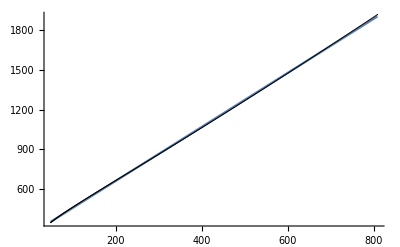

253.217+2.04257 P0

```mathematica
fitted=Fit[dataInnerCore,{1,P0},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em8=fitted
```

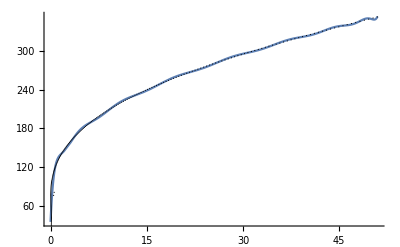

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em8=fitted;
```

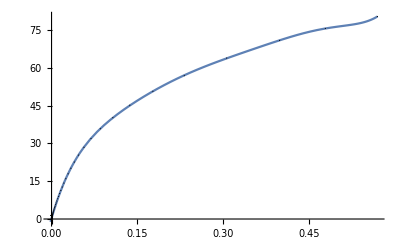

0.25228+785.624 P0-7097.19 P0^2+44787.8 P0^3-170675. P0^4+375798. P0^5-438222. P0^6+208628. P0^7

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em8=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em8=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

#### Cek hasilnya

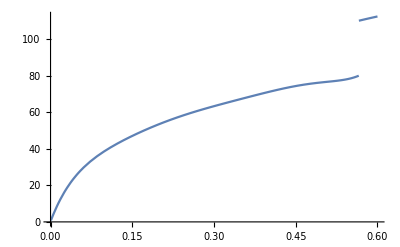

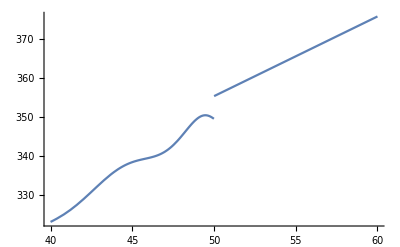

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em8;
FED2[P0_]=fitOuterCoreGUP1Em8;
FED3[P0_]=fitInnerCrustGUP1Em8;
FED4[P0_]=fitOuterCrustGUP1Em8;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em8//FortranForm
```

253.2167266972223 + 2.042574552844379*P0

```mathematica
fitOuterCoreGUP1Em8//FortranForm
```

34.996719907638656 + 217.38861380763586*P0 - 197.7847221323045*P0**2 + 
     -  100.96604597400824*P0**3 - 31.000998206090017*P0**4 + 
     -  6.201685436984379*P0**5 - 0.8545436764597708*P0**6 + 
     -  0.08425535863251823*P0**7 - 0.006099401533513903*P0**8 + 
     -  0.000329567312119461*P0**9 - 0.000013407358939926027*P0**10 + 
     -  4.112479560545507e-7*P0**11 - 9.450222969553151e-9*P0**12 + 
     -  1.6006796160515572e-10*P0**13 - 1.9380539806762782e-12*P0**14 + 
     -  1.5862872432492548e-14*P0**15 - 7.861083316562445e-17*P0**16 + 
     -  1.7807392264595506e-19*P0**17

```mathematica
fitInnerCrustGUP1Em8//FortranForm
```

0.25227973223585715 + 785.6239013862972*P0 - 7097.193231748922*P0**2 + 
     -  44787.78752904974*P0**3 - 170674.67647877714*P0**4 + 
     -  375798.1030069276*P0**5 - 438222.42374165234*P0**6 + 
     -  208628.4521716856*P0**7

```mathematica
fitOuterCrustGUP1Em8//FortranForm
```

0.00020663104786823767 + 985.7550962048155*P0 - 
     -  6.452649548410661e6*P0**2 + 4.045493650683346e10*P0**3 - 
     -  1.2422017897554195e14*P0**4 + 1.765493095354902e17*P0**5 - 
     -  9.1529417012139e19*P0**6

### fitting energy density GUP 1Em9

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]+5]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]-4;;Dimensions[data][[1]]]];
```

#### GUP 1Em9 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[1;;LengthWhile[Transpose[data][[1]],#<50.&]+2]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]-1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

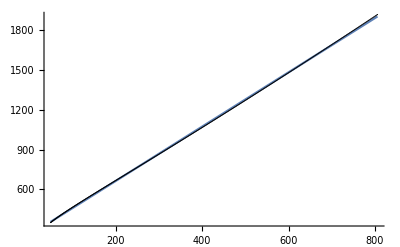

252.783+2.05087 P0

```mathematica
fitted=Fit[dataInnerCore,{1,P0},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em9=fitted
```

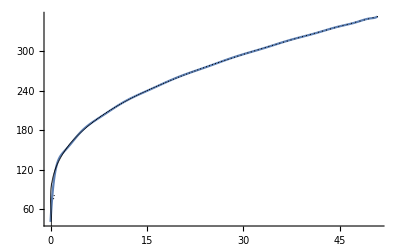

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em9=fitted;
```

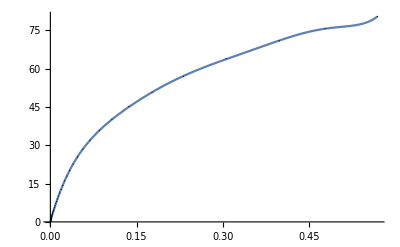

0.138753+803.312 P0-7604.05 P0^2+50338.6 P0^3-199755. P0^4+454007. P0^5-542330. P0^6+262911. P0^7

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em9=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em9=fitted
```

-Graphics-

0.000206631+985.755 P0-6.45265×10^6 P0^2+4.04549×10^10 P0^3-1.2422×10^14 P0^4+1.76549×10^17 P0^5-9.15294×10^19 P0^6

#### Cek hasilnya

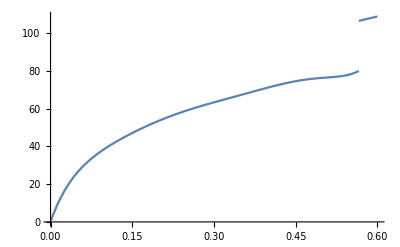

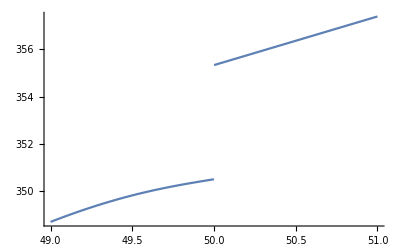

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em9;
FED2[P0_]=fitOuterCoreGUP1Em9;
FED3[P0_]=fitInnerCrustGUP1Em9;
FED4[P0_]=fitOuterCrustGUP1Em9;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,49,51},PlotRange->All]
```

```mathematica
{FED1[p],FED2[p],FED3[p],FED4[p]}/.{p->49.999713319547126}
```

{355.326,350.513,1.97058×10^17,-1.43004×10^30}

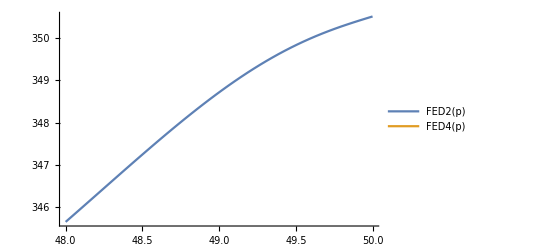

```mathematica
Plot[{FED2[p],FED4[p]},{p,48,50},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
?FortranForm
```

FortranForm[expr] prints as a Fortran language version of expr.

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em9//FortranForm
```

252.78278962148056 + 2.050868961120045*P0

```mathematica
fitOuterCoreGUP1Em9//FortranForm
```

40.15034086505595 + 177.5866219617547*P0 - 
     -  137.00971748612557*P0**2 + 61.89954941513774*P0**3 - 
     -  17.26901975343054*P0**4 + 3.19828292723069*P0**5 - 
     -  0.41368745512340627*P0**6 + 
     -  0.0386929339507851*P0**7 - 
     -  0.002678910218415325*P0**8 + 
     -  0.0001393320273523317*P0**9 - 
     -  5.4844862695484765e-6*P0**10 + 
     -  1.634623232394756e-7*P0**11 - 
     -  3.662635167044916e-9*P0**12 + 
     -  6.066820918324125e-11*P0**13 - 
     -  7.201085144548133e-13*P0**14 + 
     -  5.7902998474439245e-15*P0**15 - 
     -  2.824048011545469e-17*P0**16 + 
     -  6.305773287870958e-20*P0**17

```mathematica
fitInnerCrustGUP1Em9//FortranForm
```

0.13875280004543208 + 803.3119721991872*P0 - 7604.053978101671*P0**2 + 
     -  50338.552627037454*P0**3 - 199754.51797965978*P0**4 + 
     -  454007.45145368035*P0**5 - 542329.881379661*P0**6 + 
     -  262911.3019837204*P0**7

```mathematica
fitOuterCrustGUP1Em9//FortranForm
```

0.00020663104786823767 + 985.7550962048155*P0 - 
     -  6.452649548410661e6*P0**2 + 4.045493650683346e10*P0**3 - 
     -  1.2422017897554195e14*P0**4 + 1.765493095354902e17*P0**5 - 
     -  9.1529417012139e19*P0**6